# Trabalho Individual: Lei de Coulomb Sylvio Barreto Veras - 2019200446

## Dados 2 elétrons, cada um com carga elétrica −1, 60×10−19C, separados por uma distância d=0,1nm, obtenha as forças Coulombianas entre eles, diagramando-as vetorialmente. Use notação vetorial em toda a resolução e faça analiticamente, substituindo numericamente somente ao final.

Para calcular a força coulombiana, utilizaremos a fórmula:

```mathematica
TraditionalForm[F==k*Abs[q1*q2]/r^2]
```

F==(8.99×10^9 Abs[q1 q2])/r^2

Substituindo os valores:

```mathematica
Coulomb=HoldForm[F==8.99*10^9*Abs[1.60*10^-19*1.60*10^-19]/(0.1*10^-9)^2];
TraditionalForm[Coulomb]
```

F==(8.99 10^9 Abs[(1.6 1.6)/(10^19 10^19)])/((0.1/10^9)^2)

Calculando com o Mathematica, obtemos:

```mathematica
Coulomb //ReleaseHold
```

F==2.30144×10^-8

Agora plotaremos o gráfico da força F x distância d em que d varia de 0 a 1 nm(10^-9 m):

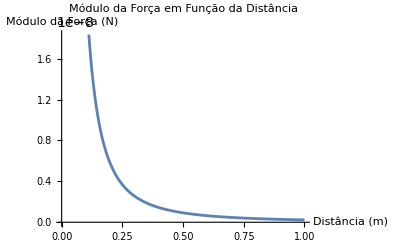

```mathematica
(*Crie o gráfico do módulo da força em função da distância*)
Plot[(8.99*10^9)*((1.60*10^-19)^2)/d^2,{d,0,1*10^-9},AxesLabel->{"Distância (m)","Módulo da Força (N)"},PlotLabel->Style[Framed["Módulo da Força em Função da Distância"],14,Gray,Background->Lighter[Yellow]]]
```